```mathematica
.20/(.01/(x/20))
```

1. x

```mathematica
Binomial[5,5]*Binomial[5,2]/Binomial[10,7]
```

1/12

```mathematica
%//N
```

0.0833333

```mathematica
Binomial[5,1]*Binomial[5,2]/Binomial[10,3]
```

5/12

```mathematica
Binomial[10,7]
```

120

```mathematica
10!
```

3628800

```mathematica
Binomial[5,3]*Binomial[5,3]/Binomial[10,6]
```

10/21

```mathematica
2*Binomial[5,1]*Binomial[5,5]/Binomial[10,6]
```

1/21

```mathematica
Entropy[2,{2,3,3,3,3,3,4,4,4,4,4,5}]//N
```

1.65002

```mathematica
?Count
```

RowBox[{"Count", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["pattern", "TI"]}], "]"}] gives the number of elements in StyleBox["list", "TI"] that match StyleBox["pattern", "TI"]. 
RowBox[{"Count", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] gives the total number of subexpressions matching StyleBox["pattern", "TI"] that appear at the levels in StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Count", "[", StyleBox["pattern", "TI"], "]"}] represents an operator form of Count that can be applied to an expression.

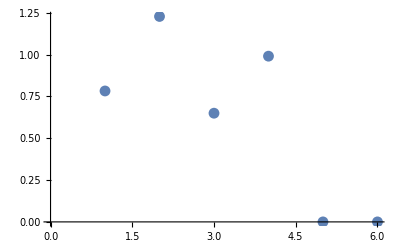

```mathematica
Table[Entropy[2,Min[#,x-#]&/@(Count[#,c]&/@Permutations[ConstantArray[c,x]~Join~ConstantArray[e,10-x]][[All,;;5]])],{x,5,10}]//ListPlot
```

```mathematica
0
```

0

```mathematica
?Entropy
```

Entropy[list] gives the base ⅇ information entropy of the values in list.
Entropy[k,list] gives the base k information entropy.

```mathematica
deck={c,c,c,c,c,c,e,e,e,e}
shuffles=Permutations[deck];
cop[shuf_]:=Sort[Count[#,c]&/@Partition[shuf,5]]
coppers=cop/@shuffles;
s=Entropy[2,coppers]
N[s]
```

{c,c,c,c,c,c,e,e,e,e}

(20 Log[21/10])/(21 Log[2])+Log[21]/(21 Log[2])

1.22858

```mathematica
Partition[shuf,5]
```

RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] partitions StyleBox["list", "TI"] into nonoverlapping sublists of length StyleBox["n", "TI"]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"]}], "]"}] generates sublists with offset StyleBox["d", "TI"]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] partitions a nested list into blocks of size SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]×SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]×… .
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["d", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["d", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] uses offset SubscriptBox[StyleBox["d", "TI"], StyleBox["i", "TI"]] at level StyleBox["i", "TI"] in StyleBox["list", "TI"]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}]}], "]"}] specifies that the first element of StyleBox["list", "TI"] should appear at position SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]] in the first sublist, and the last element of StyleBox["list", "TI"] should appear at or after position SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]] in the last sublist. If additional elements are needed, Partition fills them in by treating StyleBox["list", "TI"] as cyclic. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}], ",", StyleBox["x", "TI"]}], "]"}] pads if necessary by repeating the element StyleBox["x", "TI"]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] pads if necessary by cyclically repeating the elements SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}], ",", RowBox[{"{", "}"}]}], "]"}] uses no padding, and so can yield sublists of different lengths. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["nlist", "TI"], ",", StyleBox["dlist", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["klist", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["klist", "TI"], StyleBox["R", "TI"]]}], "}"}], ",", StyleBox["padlist", "TI"]}], "]"}] specifies alignments and padding in a nested list.